```mathematica
PATH="/Users/dibus/Documents/flo/work/HiggsPotential/RGEs/pyrate-1.0.0/";(*Replace the path of the pyrate directory*)
Get[PATH<>"SM_RGEs.m"];(*Put here the name of the file of the rges you want to solve as well as the path where it is stored*)
Get[PATH<>"/Source/Output/RunPyRate_RGEs.m"];
```

Running of RGEs provided by pyR@te is ready !

Usage:

RunRGEs[input values, Log of scale where running starts, Log of scale where running finishes, True/False (twoloop contributions)]

e.g. ￿RunRGEs[{g1→0.36,gSU2L→0.64, gSU3c→0.7},3,16,False];

```mathematica
(* Runing gauge couplings with some arbitrary values as initializaiton *)
```

```mathematica
sol=RunRGEs[{g1->0.36,gSU2L->0.64, gSU3c->0.7,Lambda1->0.07},3,16];
```

```mathematica
AllParameters
```

{gSU2L,g1,gSU3c,Yu[1,1],Yu[2,2],Yu[3,3],Ye[1,1],Ye[2,2],Ye[3,3],Yd[1,1],Yd[2,2],Yd[3,3],mu1,Lambda1}

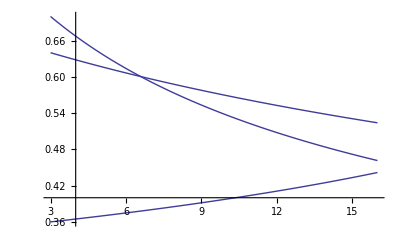

```mathematica
Plot[{g1[t],gSU2L[t],gSU3c[t]}/. sol[[1]],{t,3,16}]
```

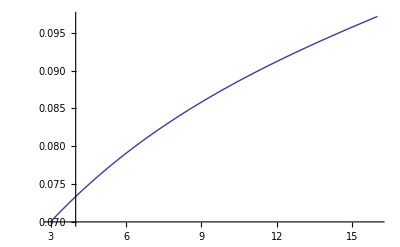

```mathematica
Plot[{Lambda1[t]}/. sol[[1]],{t,3,16}]
```

```mathematica
(* Setting values for top Yukawa and Lambda at 1 TeV *)
```

```mathematica
sol=RunRGEs[{g1->0.36,gSU2L->0.64, gSU3c->0.7,Lambda1->0.5, Yu[3,3]->0.9},3,16];
```

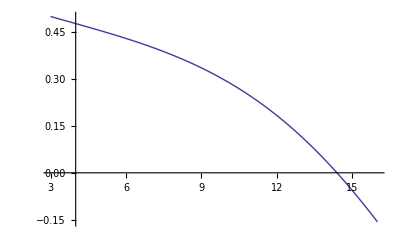

```mathematica
Plot[{Lambda1[t]}/. sol[[1]],{t,3,16}]
```